```mathematica
Clear["Global`*"]
Subscript[σ, sl]=1; Subscript[σ, lg]=2; Subscript[σ, sg]=3;

A={{1,1/2,1/2},{1/2,1,1/2},{1/2,1/2,1}}
d=0.01;
(*fs[x_,y_]:=0.5*(1-Tanh[x/d]);
fl[x_,y_]:=(1-fs[x,y])*0.5*(1+Tanh[(x^2+y^2-1)/d]);*)
(*fs[x_,y_]:=If[x>0,0,1];
fl[x_,y_]:=If[x>0,If[x^2+y^2>1,1,0],0];*)
fg[x_,y_]:=1-fs[x,y]-fl[x,y]
```

{{1,1/2,1/2},{1/2,1,1/2},{1/2,1/2,1}}

```mathematica
X={fl[x,y]+fg[x,y],fg[x,y]+fs[x,y],fl[x,y]+fs[x,y]}
```

{1-fs[x,y],1-fl[x,y],fl[x,y]+fs[x,y]}

```mathematica
LinearSolve[A,{1,0,0}]
```

{3/2,-1/2,-1/2}

```mathematica
B=Inverse[A]
```

{{3/2,-1/2,-1/2},{-1/2,3/2,-1/2},{-1/2,-1/2,3/2}}

```mathematica
FullSimplify[B.X]
(*fun[fl_,fs_]:={1-2 fs,1-2 fl,-1+2 fl+2 fs}*)
```

{1-2 fs[x,y],1-2 fl[x,y],-1+2 fl[x,y]+2 fs[x,y]}

```mathematica
fun[1/3,1/3]
```

fun[1/3,1/3]

```mathematica
fun[fl,sd]
```

fun[fl,sd]

```mathematica
fs
```

fs

```mathematica
Plot3D[{fs[x,y], fl[x,y], fg[x,y]},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[{(fl[x,y]+fg[x,y]),(fg[x,y]+fs[x,y]),(fl[x,y]+fs[x,y])},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[{1-2 fs[x,y],1-2 fl[x,y],-1+2 fl[x,y]+2 fs[x,y]},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[{fl[x,y]+fg[x,y](*,fg[x,y]+fs[x,y],fl[x,y]+fs[x,y]*)},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
A={{1,1,0,0},{1,0,1,0},{1,0,0,1},{0,1,1,0},{0,1,0,1},{0,0,1,1}}
b = {Subscript[σ, 12],Subscript[σ, 13],Subscript[σ, 14],Subscript[σ, 23],Subscript[σ, 24],Subscript[σ, 34]}
xs = {Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4]}
LinearSolve[A,b]
```

{{1,1,0,0},{1,0,1,0},{1,0,0,1},{0,1,1,0},{0,1,0,1},{0,0,1,1}}

{σ_12,σ_13,σ_14,σ_23,σ_24,σ_34}

{σ_1,σ_2,σ_3,σ_4}

{}

```mathematica
A={{1,1,0},{1,0,1},{0,1,1}}
b = {Subscript[σ, 12],Subscript[σ, 13],Subscript[σ, 23]}
LinearSolve[A,b]
```

{{1,1,0},{1,0,1},{0,1,1}}

{σ_12,σ_13,σ_23}

{1/2 (σ_12+σ_13-σ_23),1/2 (σ_12-σ_13+σ_23),1/2 (-σ_12+σ_13+σ_23)}

```mathematica
A={{1,1,0},{1,0,1},{0,1,1}}
b = {Subscript[σ, ls],Subscript[σ, lg],Subscript[σ, sg]}
sigma=LinearSolve[A,b]
```

{{1,1,0},{1,0,1},{0,1,1}}

{σ_ls,σ_lg,σ_sg}

{1/2 (σ_lg+σ_ls-σ_sg),1/2 (-σ_lg+σ_ls+σ_sg),1/2 (σ_lg-σ_ls+σ_sg)}

```mathematica
sigma
```

{1/2 (σ_lg+σ_ls-σ_sg),1/2 (-σ_lg+σ_ls+σ_sg),1/2 (σ_lg-σ_ls+σ_sg)}

```mathematica
f[r_]:=1/2*(1-Tanh[(r-r0)/d]);
D[f[r],{r,2}]+D[f[r],r]/r
```

-Sech[(r-r0)/d]^2/(2 d r)+(Sech[(r-r0)/d]^2 Tanh[(r-r0)/d])/d^2

```mathematica
DSolve[{p''[r]+p'[r]/r==(σ/r0)*(D[f[r],{r,2}]+D[f[r],r]/r)},p[r],r]
```

{{p[r]→C[2]+C[1] Log[r]-(σ Tanh[(r-r0)/d])/(2 r0)}}

```mathematica
p[r_]:=-(σ Tanh[(r-r0)/d])/(2 r0)
```

```mathematica
Err[r_]:=p''[r]+p'[r]/r-(σ/r0)*(D[f[r],{r,2}]+D[f[r],r]/r)
```

```mathematica
FullSimplify[Err[r]]
```

0

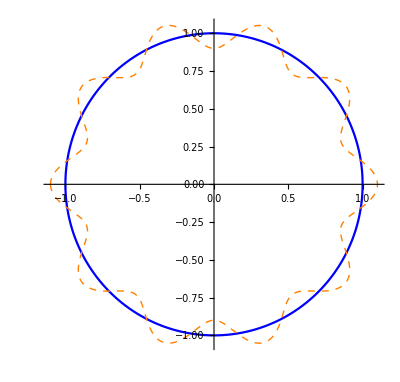

```mathematica
PolarPlot[{1,1+1/10 Cos[10t]},{t,-Pi,Pi},PlotStyle->{Blue,Directive[Dashed,Thick,Orange]}]
```

```mathematica
Export["test.eps",PolarPlot[{1,1+1/10 Cos[10t]},{t,-Pi,Pi},PlotStyle->{Blue,Directive[Dashed,Thick,Orange]}]]
```

test.eps

```mathematica
Export["test.png",PolarPlot[{1,1+1/10 Sin[10t]},{t,0,2Pi},PlotStyle->{Green,Directive[Dashed,Thick,Orange]}]]
```

test.png

```mathematica
Directory[]
```

/Users/weugene

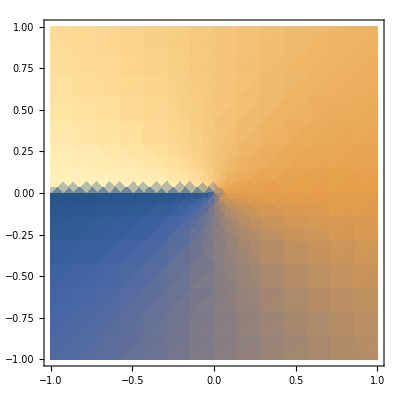

```mathematica
DensityPlot[2*ArcTan[y/(x+Sqrt[x^2+y^2])], {x,-1,1}, {y,-1,1}]
```